```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metaStructure2={Number,Number,Number,Number,Number,Number,Number,Word,Real};
metaStructure3=Real;
descdat=ReadList[StringJoin[descDir,seperator,"desc3.dat"],metaStructure2];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
tsst=35;tsend=380;tsint=15;
tfdistal=Table[{},{k,1,((tsend-tsst)/tsint)+1}];
tfdistcu=Table[{},{k,1,((tsend-tsst)/tsint)+1}];
For[ts=tsend,ts≤tsend,ts+=tsint,
icou=Ceiling[((ts-tsst)/tsint)+1];
Print["Executing ts = ",ts," , i = ",icou];
tfdistal[[icou]]=ReadList[StringJoin[AscDir,seperator,"NStar",seperator,"aluminumElectrode",seperator,"tfSamples_",ToString[ts],"sec.dat"],metaStructure3];
tfdistcu[[icou]]=ReadList[StringJoin[AscDir,seperator,"NStar",seperator,"copperElectrode",seperator,"tfSamples_",ToString[ts],"sec.dat"],metaStructure3];
(***)

];
```

Executing ts = 380 , i = 24

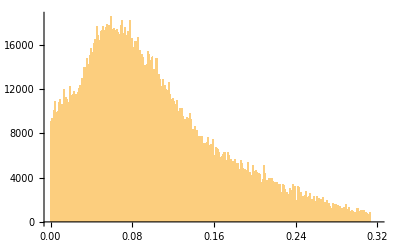

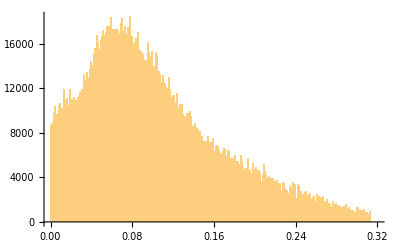

```mathematica
Histogram[tfdistal[[24]],{0,.32,.001}]
Histogram[tfdistcu[[24]],{0,.32,.001}]
```

```mathematica
histal=HistogramList[tfdistal[[24]],{0,.32,.001}];
histalt=Transpose[{(histal[[1]][[;;-2]]+(histal[[1]][[2]]-histal[[1]][[2]])/2),histal[[2]][[;;]]}];
NonlinearModelFit
```

```mathematica
Mean[tfdistal[[24]]]
Mean[tfdistcu[[24]]]
StandardDeviation[tfdistal[[24]]]
StandardDeviation[tfdistcu[[24]]]
```

0.100381

0.102369

0.0672953

0.0675591

## Tests

```mathematica
descdattf=MapThread[Append,{MapThread[Append,{MapThread[Append,{MapThread[Append,{descdat,tf}],tferr}],tf2}],tf2err}];
EDAListPlot[pttfal,Joined->True,Frame->True,FrameLabel->{"t_s(s)","t_f(s)"},PlotRange->{{20,390},{0.05,.1}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
```